### Determinant and Volume

```mathematica
Ds3D=({{x1-x4, x2-x4, x3-x4}, {y1-y4, y2-y4, y3-y4}, {z1-z4, z2-z4, z3-z4}})/.{z4->-z1-z2-z3,y4->-y1-y2-y3,x4->-x1-x2-x3};
Ds2D=({{x1-x3, x2-x3}, {y1-y3, y2-y3}});
a=√((x3-x1)^2+(y3-y1)^2);
b=√((x3-x2)^2+(y3-y2)^2);
c=√((x1-x2)^2+(y1-y2)^2);
s=(a+b+c)/2;
Vh=√(s(s-a)(s-b)(s-c));
FullSimplify[{Vh,Det[Ds2D]},Reals]
```

{1/2 Abs[x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3)],x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)}

```mathematica
λ[k_,ν_]=(k ν)/((1+ν)(1-2ν));
μ[k_,ν_]=k/(2(1+ν));
LameCoefficients[κ_,ν_]={λ[k,ν], μ[k,ν]};
```

```mathematica
N@Solve[λ[1, ν]==1,ν]
λ[1.0,0.33]
μ[1.0,0.33]
```

{{ν→-1.36603},{ν→0.366025}}

0.729766

0.37594

```mathematica
$Assumptions=_∈Reals;
Id= IdentityMatrix[2];
VenantKirchhoffPotential[F_,k_,ν_]:=Module[{E},
E=1/2(Fᵀ.F-Id);
μ[k,ν]Tr[E.E]+λ[k,ν]/2 Tr[E]^2
]
VenantKirchhoffStress[F_,k_,ν_]:=Module[{E},
E=1/2(Fᵀ.F-Id);
F.(2 μ[k,ν] E+λ[k,ν] Tr[E] Id)
]
VenantKirchhoffStressDifferential[F_,dF_,k_,ν_]:=Module[{E,dE},
E=1/2(Fᵀ.F-Id);dE=1/2(dFᵀ.F+Fᵀ.dF);
dF.(2 μ[k,ν] E+λ[k,ν] Tr[E] Id)+F.(2 μ[k,ν] dE+λ[k,ν] Tr[dE] Id)
]
Ds[tr_]:=Transpose[tr[[1;;2]]-{tr[[3]],tr[[3]]}];
Bm[tr_]:=Inverse[Ds[tr]]

ElasticForce[P_,vA_]:=Module[{H},
H=-Abs[Det[Ds[vA]]]P.(Inverse[Ds[vA]])ᵀ;
{Hᵀ[[1]],Hᵀ[[2]],-Hᵀ[[1]]-Hᵀ[[2]]}
]
F[vA_,vB_]:=Ds[vB].Bm[vA];
ScanLine[α_,v_,vA_,k_,ν_]:=Module[{P,f},
f=ElasticForce[VenantKirchhoffStress[F[vA,v],k,ν],vA];
P=VenantKirchhoffStress[F[vA,v+α f],k,ν];
{-Flatten[ElasticForce[P,vA]].Flatten[f],
VenantKirchhoffPotential[F[vA,v+α f],k,ν],f}
]
W[x_]:=Area[Simplex[x]];
```

```mathematica
efT=Module[{xT,XT},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
-W[XT]2Table[D[VenantKirchhoffPotential[F[XT,xT],k,ν],x[i]],{i,1,6}]
];
eKT[XX_,xx_,k_,ν_]=Module[{xT,XT},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
-W[XT]2Table[D[VenantKirchhoffPotential[F[XT,xT],k,ν],x[i],x[j]],{i,1,6},{j,1,6}]/.{x[i_]-> xx[[i]],X[i_]->  XX[[i]]}
];

fT=Module[{xT,XT},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
Flatten[ElasticForce[VenantKirchhoffStress[F[XT,xT],k,ν],XT]]
];

kT=Table[D[fT[[i]],x[j]],{i,1,6},{j,1,6}];
fT/.{k->1,ν->0.33,x[i_]-> {1,2,3,-4,5,6}[[i]],X[i_]->  {2,4,1,5,2,9}[[i]]}
efT/.{k->1,ν->0.33,x[i_]-> {1,2,3,-4,5,6}[[i]],X[i_]->  {2,4,1,5,2,9}[[i]]}
eKT [ {2,4,1,5,2,9},{1,2,3,-4,5,6},1,0.33]
temp=kT/.{k->1,ν->0.33,x[i_]-> {1,2,3,-4,5,6}[[i]],X[i_]->  {2,4,1,5,2,9}[[i]]};
Chop[temp-Transpose[temp]]//MatrixForm
```

{172.864,-923.543,-201.366,1185.98,28.5021,-262.442}

{172.864,-923.543,-201.366,1185.98,28.5021,-262.442}

{{-121.335,42.3055,147.609,-51.0075,-26.274,8.70199},{42.3055,-325.79,-48.743,406.043,6.43751,-80.2537},{147.609,-48.743,-185.29,59.2481,37.6807,-10.5051},{-51.0075,406.043,59.2481,-517.178,-8.2406,111.135},{-26.274,6.43751,37.6807,-8.2406,-11.4066,1.8031},{8.70199,-80.2537,-10.5051,111.135,1.8031,-30.8812}}

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dimensions[fT]
```

{6}

```mathematica
v={{0,0},{0,1},{1,0}}
Ds[v]//MatrixForm
Bm[v]//MatrixForm
```

{{0,0},{0,1},{1,0}}

(-1 | -1
0 | 1)

(-1 | -1
0 | 1)

```mathematica
vA={{0,0},{0,1},{1,0}};
vB={{0,-1},{2,2},{1,-1}};
vInit = vA+0.7{{0,1},{0,0},{0,0}};
dv={{1,0},{0,1},{1,1}};
s=VenantKirchhoffStress[F[vA,vB],1,0.33]
ds=VenantKirchhoffStressDifferential[F[vA,vB],F[vA,dv],1,0.33]
ds2=VenantKirchhoffStressDifferential[F[vA,vInit],F[vA,dv],1,0.33]
ψ=VenantKirchhoffPotential[F[vA,vB],1,0.33]
F[vA,vB]
g=Partition[Flatten@ElasticForce[s,vA],1]
Partition[Flatten@ElasticForce[ds,vA],1]
Partition[Flatten@ElasticForce[ds2,vA],1]
```

{{5.88235,18.5316},{2.25564,26.6696}}

{{1.48165,-5.1747},{7.38611,14.0867}}

{{-0.739275,-0.0309598},{0.366873,-0.225785}}

27.4215

{{1,2},{0,3}}

{{24.414},{28.9253},{-18.5316},{-26.6696},{-5.88235},{-2.25564}}

{{-3.69306},{21.4728},{5.1747},{-14.0867},{-1.48165},{-7.38611}}

{{-0.770234},{0.141088},{0.0309598},{0.225785},{0.739275},{-0.366873}}

-1

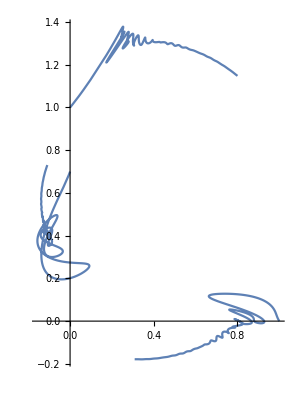

```mathematica
t1=100;
system[t_]=Table[i[j][t],{j,1,3},{i,{xc,yc}}];
Det[Ds[vA]]
rhs=ElasticForce[VenantKirchhoffStress[F[vA,system[t]],1, 0.33],vA]+
0.1ElasticForce[VenantKirchhoffStressDifferential[F[vA,system[t]],F[vA,system'[t]],1,0.33],vA]+
0.0{{0,0},{0,Cos[0.5t]},{0,0}};
lhs=system''[t];

y[t_]=system[t];


sol[t_]=NDSolve[{lhs==rhs,
y[0]==vInit,y'[0]==0vInit},y[t],{t,0,t1}];
Animate[
Graphics[{PointSize[0.05],Polygon[(system[t]/.sol[t][[1]])],
Point[(system[t]/.sol[t])[[1]],VertexColors->{Red, Green, Blue}]}
,Frame->True,PlotRange->{{-2,2},{-2,2}}],{t,0,t1}]
ParametricPlot[system[t]/.sol[t],{t,0,t1}]
```

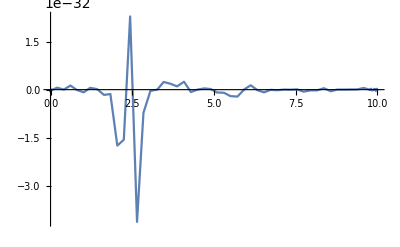

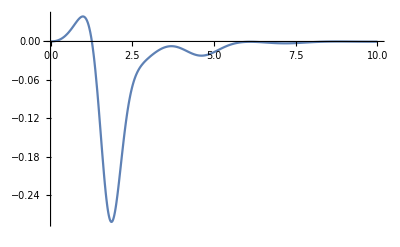

{{-1.63762,0.62339,0.00691549,0.140559,1.6307,-0.76395},{0.62339,0.103469,-0.0400126,-0.368206,-0.583378,0.264737},{0.00691549,-0.0400126,0.024617,0.174932,-0.0315325,-0.13492},{0.140559,-0.368206,0.174932,0.00733759,-0.315492,0.360869},{1.6307,-0.583378,-0.0315325,-0.315492,-1.59917,0.898869},{-0.76395,0.264737,-0.13492,0.360869,0.898869,-0.625605}}

{-0.630306,-0.0634568,0.0153956,0.193274,0.61491,-0.129817}

{1.74207×10^-40,0.0390234,-0.256976,-0.0255894,-0.0109413,-0.0166951,-0.000616433,-0.0027689,-0.00110321,-0.000112327,-0.000360891}

-0.172048

```mathematica
K[t_]:=(Table[UnitVector[6,i].Flatten[ElasticForce[VenantKirchhoffStressDifferential[F[vA,system[t]/.sol[t][[1]]],F[vA,Partition[UnitVector[6,j],2]],1,0.33],vA]],{i,1,6},{j,1,6}]);
V[t_]:=D[system[u]/.sol[u][[1]],u]/.u->t
Plot[Det[eKT[Flatten[vA],Flatten[system[t]/.sol[t]],1,0.33]],{t,0,10},PlotRange->Full]
Plot[Flatten[V[t]].K[t].Flatten[V[t]],{t,0,10},PlotRange->Full]
K[1]
K[1].Flatten[dv]
Table[Flatten[V[t]].K[t].Flatten[V[t]],{t,0,10,1}]
Flatten[dv].K[0].Flatten[dv]
```

1.

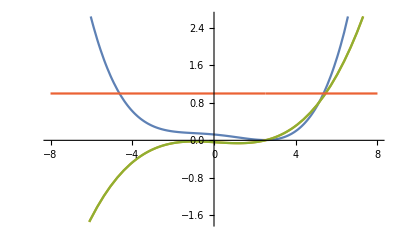

```mathematica
bla=ScanLine[α,vInit,vA,1,0.33];
en=bla[[2]];
den1=D[en,α];
den2=bla[[1]];
FullSimplify[den2/den1]
Plot[{en,den1,den2,den2/den1},{α,-8,8}]
```

```mathematica
m=Module[{m},
m=RandomInteger[{-5,5}, {6,6}];
m=(m+mᵀ);
While[Not[IndefiniteMatrixQ[m]],
m=RandomInteger[{-5,5}, {6,6}];
m=(m+mᵀ);
];
m
]
b=RandomInteger[{-10, 10},{6,1}]
Partition[N@LinearSolve[m,Flatten[b]],1]
```

{{-2,5,0,-3,3,2},{5,8,3,8,9,-2},{0,3,0,-1,6,0},{-3,8,-1,-8,-2,2},{3,9,6,-2,-6,-2},{2,-2,0,2,-2,-6}}

{{10},{1},{-2},{-8},{-6},{3}}

{{-15.4162},{0.530737},{6.62842},{5.37832},{0.297684},{-4.12211}}

```mathematica
m={{10,0,4,-2,1,0},{0,6,0,0,5,0},{4,0,6,-1,-1,2},{-2,0,-1,10,5,2},{1,5,-1,5,10,-1},{0,0,2,2,-1,6}}
b={-4,-9,-9,10,3,-9};
PositiveDefiniteMatrixQ[m]
N@Eigenvalues[m]
CholeskyDecomposition[m]//MatrixForm
Partition[b,1]
Partition[N@Inverse[m].b,1]
```

{{10,0,4,-2,1,0},{0,6,0,0,5,0},{4,0,6,-1,-1,2},{-2,0,-1,10,5,2},{1,5,-1,5,10,-1},{0,0,2,2,-1,6}}

True

{16.6969,12.9072,9.31561,5.72771,2.51595,0.836613}

(√10 | 0 | 2 √(2/5) | -√(2/5) | 1/(√10) | 0
0 | √6 | 0 | 0 | 5/(√6) | 0
0 | 0 | √(22/5) | -1/(√110) | -7/(√110) | √(10/11)
0 | 0 | 0 | √(211/22) | 113/(√4642) | 23 √(2/2321)
0 | 0 | 0 | 0 | √(1606/633) | -313 √(3/338866)
0 | 0 | 0 | 0 | 0 | √(6051/1606))

{{-4},{-9},{-9},{10},{3},{-9}}

{{0.0223104},{-2.05611},{-0.784498},{0.876219},{0.667328},{-1.41935}}

```mathematica
FullSimplify[Det[Table[x[i,j],{i,1,3},{j,1,3}]+Table[x[j,i],{i,1,3},{j,1,3}]]]
```

-(x[2,3]+x[3,2]) (-(x[1,2]+x[2,1]) (x[1,3]+x[3,1])+2 x[1,1] (x[2,3]+x[3,2]))+(x[1,3]+x[3,1]) (-2 x[2,2] (x[1,3]+x[3,1])+(x[1,2]+x[2,1]) (x[2,3]+x[3,2]))+2 (-(x[1,2]+x[2,1])^2+4 x[1,1] x[2,2]) x[3,3]